generatenewvoronoi

```mathematica
(*general Parameters*)
SetDirectory[NotebookDirectory[]];
(*the equations of motion are non-dimensionalized so these values don't matter much.*)
a=225;
b=225;
x0=0;
y0=0;
d = Sqrt[a^2-b^2];
center={x0,y0};
focus1={x0-d, y0};
focus2 ={x0+d, y0} ;

nCells = 320;
scale = Sqrt[41.3083/(Pi*a*b/nCells)]; (*one length unit equals scale*micron. Based on mean observed cell area in our drosophila*)
originalNCells = nCells;
ellipsePointList = Table[{a*Cos[θ],b*Sin[θ]},{θ,0,2π,2π/200}];
(*replace with your directory address for the generator file. In the Github*)
Import["C:\\Users\\kaden\\OneDrive\\Desktop\\Hutson Lab Research\\voronoiDiagramGenerator (5).m"]
tAnneal=1500;
μ=30;
timeConstant = 0.8969476207347036;(*loosely constrained by measurements from Ivy Han et al 2024. Loose because recoil ablations are out of equilibrium and therefore not very well described by the vertex model*)
intercolationProportion = 0.01; (*trade off here--lower makes it so the cells don't get stuck in intercolation loops, but too low and things get really computationally expensive*)
nonDimensionalizedContractileConstant = 0.01771; (*determined by equilibrated values post ablation from Ivy Han et al 2024. More tightly constrained*)
outerTension = 0.14; (*constrained by Bonnet et al circular wound experiments from 2012*)
lineTensionVariability =0.00093; (*tuned to produce near zero intercolation counts in control tissues*)
shP = 3.745; (* tuned to produce near zero intercolation counts and reasonable shape parameter values when compared to real tissue*)
decayRate =150; (*Tetley value, based on actin turnover times*)
(*healing Parameters*)
damageFn[rad_] :=(
scaledRadius = (rad/originalScale)/woundScale;
0.48*(Erf[-(scaledRadius-0.72)/0.16]+1));
tResponse = 700; (*based on when wound starts pulling*)
pull =0.115;(*tuned in conjunction with wound tension to produce reasonable closure times with linear in area closure rates. Pull corresponds to purse string tension while woundTension corresponds to crawling force*)
tHealing =75000;
woundTension = 0.13;

Import["C:\\Users\\kaden\\Downloads\\voronoiDiagramFunctions internal pressure (1) (1).wl"];
Print["voronoi Function Defined"];
(*this file is also in the github*)


(*implementing line tension as in tetley, but with mean line tensions set to create an effective target perimeter for each cell*)
contractileTension =Table[nonDimensionalizedContractileConstant,{i,Length[cellularVoronoiDiagram[[2]]]}];
meanTensionCell = Table[(contractileTension[[i]]/originalScale)*(-P0s[[i]]),{i,Length[P0s]}];
meanTensionEdge = Table[Total[meanTensionCell[[getCellsAdjacentToEdge[edgeData[[All,2]][[i]],cellularVoronoiDiagram]]] ],{i,Length[edgeData[[All,  2]]]}];
tMax = Max[{tHealing,tAnneal}]+200;
```

voronoi Function Defined

```mathematica
lineTensions = Table[
proc = ItoProcess[ⅆlineTension[t]== -1/decayRate*(lineTension[t]-meanTensionEdge[[i]])ⅆt+ⅆw[t],lineTension[t],{lineTension,meanTensionEdge[[i]]},t,w\[Distributed]WienerProcess[0,lineTensionVariability]];
Subscript[compiled, i]=Compile[{t},Evaluate[Interpolation[RandomFunction[proc,{0,tMax,5}]][t]]];
With[{compiled = Subscript[compiled, i]},Subscript[f, i][t_?NumericQ]:=compiled[t]];
With[{f = Subscript[f, i]},HoldForm[f[t]]],
{i,Length[edgeData]}];
healths = Table[1,{i,Length[cellularVoronoiDiagram[[2]]]}];
Print["linetensionscreated"];
(*prep for the diffeq solver*)
nVertices = Length[vertexList];
tCurrent = 0;
Subscript[vertexLists, 0]=vertexList;
Subscript[timeStop, 0 ] = 0;
Subscript[cellularVoronoiDiagrams, 0] = cellularVoronoiDiagram;
Subscript[edgeDatas, 0] = edgeData;
stepSize =0.0000001;
(*Annealing Step, no cells should be deleted (it will throw an error if there are)*)
```

linetensionscreated

Anneal

```mathematica
SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->10.];
solutions = {};
Do[
diffEQs = D[Flatten[vertexList],t] == Flatten[Table[(1/μ)*forceOnVertexSolved[i,cellularVoronoiDiagram,vertexList,A0s,contractileTension,lineTensions,edgeData,healths],{i,Length[vertexList]}]];
bcList = Flatten[vertexList/.t->tCurrent]== Flatten[cellularVoronoiDiagram[[1]]];

intercolation = False;
Timing[times={};
Monitor[
s=NDSolve[{ReleaseHold[diffEQs], bcList,With[{edgeData = edgeData, vertexList = vertexList},WhenEvent[#-intercolationLength<0, 
(cellularVoronoiDiagram[[1]] = Table[{vertexList[[i,1]],vertexList[[i,2]]},{i,Length[vertexList]}];
intercolatedEdge = Position[edgeData[[All,1]],#][[1]][[1]];

Print["intercolating ",intercolatedEdge];
tCurrent = t;
intercolation = True;

"StopIntegration"
),"DetectionMethod"->"Sign"]&/@edgeData[[All,1]]]},Flatten[vertexList],{t,tCurrent,tAnneal},StartingStepSize->stepSize,AccuracyGoal->3, PrecisionGoal->4,Method->"StiffnessSwitching",MaxStepSize->Infinity,EvaluationMonitor:>AppendTo[times,t],MaxStepFraction->Infinity,InterpolationOrder->1];,times[[-1]] ];
];
stepSize = (Subscript[x, 1][t]/. s[[1]]/.{t->"Coordinates"}//First//Differences)[[-1]];
AppendTo[solutions,s];
numIntercolations = j-1;
Subscript[timeStop, j] = tCurrent;
If[!intercolation ,cellularVoronoiDiagram[[1]] = (Table[{vertexList[[i,1]],vertexList[[i,2]]},{i,Length[vertexList]}]/.s/.t->tCurrent)[[1]];Break[]];
tempCenter = Mean[{cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[1]]]],cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[2]]]]}];newEdge =r[((cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[1]]]]-cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[2]]]])/Norm[cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[1]]]]-cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[2]]]]])*(intercolationLength+1)];
intercolate[edgeData[[intercolatedEdge]]];cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[1]]]]=(tempCenter+0.5*newEdge );cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[2]]]]=(tempCenter-0.5*newEdge);
If[boundaryEdge,
newTension =(1/(originalScale))*(-contractileTension[[cellList[[3]][[1]]]]*P0s[[cellList[[3]][[1]]]]-contractileTension[[cellList[[4]][[1]]]]*P0s[[cellList[[4]][[1]]]]);,

If[didRun,
newTension = (contractileTension[[cellList[[3]][[1]]]]/originalScale)*(-P0s[[cellList[[3]][[1]]]]);,

newTension = (1/(originalScale))*(-contractileTension[[cellList[[3]][[1]]]]*P0s[[cellList[[3]][[1]]]]-contractileTension[[cellList[[4]][[1]]]]*P0s[[cellList[[4]][[1]]]]);
];
];
 proc = ItoProcess[ⅆlineTension[t]== -1/decayRate*(lineTension[t]-newTension)ⅆt+ⅆw[t],lineTension[t],{lineTension,newTension},t,w\[Distributed]WienerProcess[0,lineTensionVariability]];
Subscript[compiled, i]=Compile[{t},Evaluate[Interpolation[RandomFunction[proc,{0,tMax,5}]][t]]];
With[{compiled = Subscript[compiled, i]},Subscript[f, i][t_?NumericQ]:=compiled[t]];
intercolatedLineTension =With[{f = Subscript[f, i]},HoldForm[f[t]]];
lineTensionIntercolated=intercolatedLineTension;
lineTensions = Insert[Delete[lineTensions,intercolatedEdge],lineTensionIntercolated,intercolatedEdge];
Subscript[cellularVoronoiDiagrams, j] = cellularVoronoiDiagram;
Subscript[edgeDatas, j] = edgeData;
Subscript[vertexLists, j] = vertexList,

{j,40000}];
Print["Annealing Complete"];
solutionTable=Table[vertexList/.solutions[[i]][[1]],{i,Length[solutions]}];
Subscript[timeStop, numIntercolations+1] = tAnneal;
cellularVoronoiDiagram[[1]] = solutionTable[[numIntercolations+1]]/.t->tAnneal;
```

Wounding

```mathematica
(*wound post annealing*)
nCells = Length[cellularVoronoiDiagram[[2]]];
solutionTable=Table[vertexList/.solutions[[i]][[1]],{i,Length[solutions]}];
Subscript[timeStop, numIntercolations+1] = tAnneal;
cellularVoronoiDiagram[[1]] = solutionTable[[numIntercolations+1]]/.t->tAnneal;
```

```mathematica
ablateCells[woundList_]:=(
currentWoundList = Sort[woundList];
woundNum = currentWoundList[[1]];
Do[
neighboringDeletions = Intersection[getNeighboringCells[woundNum,cellularVoronoiDiagram],currentWoundList];
vertexCount = Length[cellularVoronoiDiagram[[2]][[#]][[2]]]&/@neighboringDeletions;
nextBreakdownIndex = Ordering[vertexCount,1][[1]];
nextBreakdown = neighboringDeletions[[nextBreakdownIndex]];
borderBreakdown[{woundNum,nextBreakdown}];
woundListIndex = Position[currentWoundList,nextBreakdown][[1,1]];
currentWoundList = Delete[currentWoundList,woundListIndex];
currentWoundList [[woundListIndex;;]] = currentWoundList [[woundListIndex;;]]-1
,{i,Length[woundList]-1}];
healths[[woundNum]] = 0;
contractileTension[[woundNum]] = 0;
meanTensionCell = Table[(contractileTension[[i]]/originalScale)*(-P0s[[i]]),{i,Length[P0s]}];
meanTensionEdge = Table[Total[meanTensionCell[[getCellsAdjacentToEdge[edgeData[[All,2]][[i]],cellularVoronoiDiagram]]] ],{i,Length[edgeData[[All,2]]]}];
increasingLineTension=Piecewise[{{pull*t/tResponse,0<=t<tResponse},{pull(*+pull*(1-(t-tResponse)/(10350-tResponse))/3*),t>=tResponse}}];
lineTensions = Table[
proc = ItoProcess[ⅆlineTension[t]== -1/decayRate*(lineTension[t]-meanTensionEdge[[i]])ⅆt+ⅆw[t],lineTension[t],{lineTension,meanTensionEdge[[i]]},t,w\[Distributed]WienerProcess[0,lineTensionVariability]];
Subscript[compiled, i]=Compile[{t},Evaluate[Interpolation[RandomFunction[proc,{0,tMax,5}]][t]]];
With[{compiled = Subscript[compiled, i]},Subscript[f, i][t_?NumericQ]:=compiled[t]];
With[{f = Subscript[f, i]},HoldForm[f[t]]],
{i,Length[edgeData]}];
Table[lineTensions[[i]]=lineTensions[[i]]+increasingLineTension,{i,getCellEdges[woundNum]}];
nVertices = Length[vertexList];
)
```

```mathematica
woundList = Select[Range[Length[cellularVoronoiDiagram[[2]]]],Or[Evaluate[Sequence@@(Norm[#]<(30/(scale))&/@cellularVoronoiDiagram[[1]][[cellularVoronoiDiagram[[2]][[#]][[2]]]])]]&]
```

{11,21,23,26,31,36,37,45,50,51,52,54,62,68,72,77,82,84,91,97,99,105,107,110,112,113,116,119,125,128,132,133,137,145,149,153,155,159,168,171,172,177,185,194,195,198,201,206,209,213,216,218,223,230,234,235,237,238,239,249,253,272,281,283,284,285,291,297,300,303,311,314,315}

```mathematica
ablateCells[woundList]
Export["woundedvoronoi8.csv",cellularVoronoiDiagram]
```

woundedvoronoi8.csv

saved wounded voronoi

```mathematica
(*general Parameters. See comments in "generate new voronoi" for more explanation*)
SetDirectory[NotebookDirectory[]];
a=225;
b=225;
x0=0;
y0=0;
d = Sqrt[a^2-b^2];
center={x0,y0};
focus1={x0-d, y0};
focus2 ={x0+d, y0} ;
nCells = 280;
scale = Sqrt[41.3083/(Pi*a*b/nCells)]; (*one length unit equals scale*micron *)
originalNCells = nCells;
(*might need to modify this code if you export in a different format*)
ellipsePointList = Table[{a*Cos[θ],b*Sin[θ]},{θ,0,2π,2π/200}];
raw=Import["C:\\Users\\kaden\\Downloads\\finished_undergrad\\mathematica\\wound1","String"];
raw=StringReplace[raw,{"\""->"","\r"->",","\n"->""}];
raw = ToExpression["{"<>StringDrop[raw,-1]<>"}"];
splitPos=Position[raw,{_Integer,{__Integer}},{1},1][[1,1]];
cellularVoronoiDiagram={raw[[1;;splitPos-1]],raw[[splitPos;;]]};

tAnneal=1000;
μ=30;
timeConstant = 0.8969476207347036;
intercolationProportion = 0.01; 
nonDimensionalizedContractileConstant = 0.01771;
outerTension = 0.14;
lineTensionVariability = 0.00093; 
shP = 3.745;
decayRate =150; 
tResponse = 700; (*based on when wound starts pulling*)
pull =0.115;(*shooting for 275 ish minutes, so 16500 seconds average close time*)(*previous value--0.365*)
woundTension = 0.13;(*previous value = 0.06*)
tHealing =90000;
(*contractile wave parameters*)
timeWaveStart = 120;
tCrossover = 30;

Import["C:\\Users\\kaden\\Downloads\\finished_undergrad\\mathematica\\voronoiDiagramFunctions"];
Print["voronoi Function Defined"];
contractileTension =Table[nonDimensionalizedContractileConstant,{i,Length[cellularVoronoiDiagram[[2]]]}];
meanTensionCell = Table[(contractileTension[[i]]/originalScale)*(-P0s[[i]]),{i,Length[P0s]}];
meanTensionEdge = Table[Total[meanTensionCell[[getCellsAdjacentToEdge[edgeData[[All,2]][[i]],cellularVoronoiDiagram]]] ],{i,Length[edgeData[[All,2]]]}];
tMax = Max[{tHealing,tAnneal}]+200;
woundNum = Flatten[Ordering[A0s,-1]][[-1]];
healths = Table[1,{i,Length[cellularVoronoiDiagram[[2]]]}];
healths[[woundNum]] = 0;
contractileTension[[woundNum]] = 0;
meanTensionCell = Table[(contractileTension[[i]]/originalScale)*(-P0s[[i]]),{i,Length[P0s]}];
meanTensionEdge = Table[Total[meanTensionCell[[getCellsAdjacentToEdge[edgeData[[All,2]][[i]],cellularVoronoiDiagram]]] ],{i,Length[edgeData[[All,2]]]}];
increasingLineTension=Piecewise[{{pull*t/tResponse,0<=t<tResponse},{pull(*+pull*(1-(t-tResponse)/(10350-tResponse))/3*),t>=tResponse}}];
lineTensions = Table[
proc = ItoProcess[ⅆlineTension[t]== -1/decayRate*(lineTension[t]-meanTensionEdge[[i]])ⅆt+ⅆw[t],lineTension[t],{lineTension,meanTensionEdge[[i]]},t,w\[Distributed]WienerProcess[0,lineTensionVariability]];
Subscript[compiled, i]=Compile[{t},Evaluate[Interpolation[RandomFunction[proc,{0,tMax,5}]][t]]];
With[{compiled = Subscript[compiled, i]},Subscript[f, i][t_?NumericQ]:=compiled[t]];
With[{f = Subscript[f, i]},HoldForm[f[t]]],
{i,Length[edgeData]}];
Print["linetensionscreated"];
Table[lineTensions[[i]]=lineTensions[[i]]+increasingLineTension,{i,getCellEdges[woundNum]}];
(*prep for the diffeq solver*)
```

voronoi Function Defined

linetensionscreated

visualizations & checks. Some of these can only be run if a simulation run is in memory.

```mathematica
cellsNotOnBorders = Select[Range[Length[cellularVoronoiDiagram[[2]]]],!cellIsOnBoundary[#]&];
Mean[Table[getCellPerimeter[k]/Sqrt[getCellArea[k]],{k,cellsNotOnBorders}]]
```

3.88179

{-0.0614478,-0.0447027}

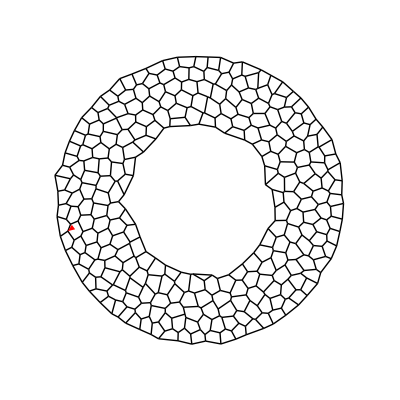

```mathematica
v = 1;
force = forceOnVertexSolved[v,cellularVoronoiDiagram,cellularVoronoiDiagram[[1]],A0s,contractileTension,ReleaseHold[lineTensions/.t->0],edgeData,healths]

Show[
{
Sequence@@Table[Graphics[{Thick,Black,Line[{(cellularVoronoiDiagram[[1]][[edgeData[[i]][[2]][[1]]]]),(cellularVoronoiDiagram[[1]][[edgeData[[i]][[2]][[2]]]])}]}],{i,Length[edgeData]}](*,
Sequence@@Table[Graphics[{Blue,Disk[cellularVoronoiDiagram[[1]][[i]],5]}],{i,cellularVoronoiDiagram[[2]][[woundNum]][[2]]}],*)
(*Graphics[{Green,Disk[cellularVoronoiDiagram[[1]][[middleEdgeVertex]],5]}],
Graphics[{Yellow,Disk[cellularVoronoiDiagram[[1]][[vertex1CCW]],5]}],
Graphics[{Blue,Disk[cellularVoronoiDiagram[[1]][[vertex3CCW]],5]}]*)
,
Graphics[{Red,Arrow[{cellularVoronoiDiagram[[1]][[v]],cellularVoronoiDiagram[[1]][[v]]+force}]}]

},PlotRange->{{-1.2a,1.2a},{-1.2b,1.2b}}
]
```

```mathematica
diagrams = Table[
Show[
{
Sequence@@Table[Graphics[{Thick,Red,Line[{(Subscript[cellularVoronoiDiagrams, j][[1]][[Subscript[edgeDatas, j][[i]][[2]][[1]]]]),(Subscript[cellularVoronoiDiagrams, j][[1]][[Subscript[edgeDatas, j][[i]][[2]][[2]]]])}]}],{i,Length[Subscript[edgeDatas, j]]}](*,
Sequence@@Table[Graphics[{Blue,Disk[cellularVoronoiDiagram[[1]][[i]],5]}],{i,cellularVoronoiDiagram[[2]][[woundNum]][[2]]}],*)
(*Graphics[{Green,Disk[cellularVoronoiDiagram[[1]][[middleEdgeVertex]],5]}],
Graphics[{Yellow,Disk[cellularVoronoiDiagram[[1]][[vertex1CCW]],5]}],
Graphics[{Blue,Disk[cellularVoronoiDiagram[[1]][[vertex3CCW]],5]}]*)


},PlotRange->{{-1.2a,1.2a},{-1.2b,1.2b}}
],{j,numIntercolations}]
```

```mathematica
diagrams = Table[
Show[
{
Sequence@@Table[Graphics[{Thick,Red,Line[{(Subscript[cellularVoronoiDiagrams, j][[1]][[Subscript[edgeDatas, j][[i]][[2]][[1]]]]),(Subscript[cellularVoronoiDiagrams, j][[1]][[Subscript[edgeDatas, j][[i]][[2]][[2]]]])}]}],{i,Length[Subscript[edgeDatas, j]]}]
(*Sequence@@Table[Graphics[{Blue,Disk[cellularVoronoiDiagram[[1]][[i]],5]}],{i,cellularVoronoiDiagram[[2]][[woundNum]][[2]]}],*)


},PlotRange->{{-1.2a,1.2a},{-1.2b,1.2b}}
],{j,numIntercolations-1}]
ListAnimate[diagrams]
```

Table::iterb: Iterator {j,-1+numIntercolations} does not have appropriate bounds.

Table[Show[{Sequence@@Table[-Graphics-,{i,Length[edgeDatas_j]}]},PlotRange→{{-1.2 a,1.2 a},{-1.2 b,1.2 b}}],{j,-1+numIntercolations}]

ListAnimate[Table[Show[{Sequence@@Table[-Graphics-,{i,Length[edgeDatas_j]}]},PlotRange→{{-1.2 a,1.2 a},{-1.2 b,1.2 b}}],{j,-1+numIntercolations}]]

```mathematica
SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->10.];
woundHealed = False;
tCurrent = 0;
Subscript[timeStop, 0 ] = 0;
Subscript[cellularVoronoiDiagrams, 0] = cellularVoronoiDiagram;
Subscript[edgeDatas, 0] = edgeData;
Subscript[vertexLists, 0] = vertexList;
Subscript[lineTensionss, 0] = lineTensions;
stepSize =0.001;
probabilityWeightSpatialBB[pair_] :=
(pairCenter = Mean[{getCentroid[pair[[1]]],getCentroid[pair[[2]]]}];
radWound = Sqrt[(getCellArea[woundNum]/π)];
distanceLE = Norm[pairCenter-getCentroid[woundNum]]-radWound;
Max[{PDF[ExtremeValueDistribution[9.524046450514108,6.429043846372746],distanceLE/scale],10^(-9)}]/( Norm[pairCenter-getCentroid[woundNum]])^2
) (*based on data from white et al. Prob should've just used kernal smoothing of the data but instead I eyeballed this fit*)
cellPickerBB[cells_] :=
(pairs = Select[Subsets[cells,{2}],Length[Intersection[cellularVoronoiDiagram[[2]][[#[[1]]]][[2]],cellularVoronoiDiagram[[2]][[#[[2]]]][[2]]]]>0&&Min[Length/@cellularVoronoiDiagram[[2]][[Intersection[getNeighboringCells[#[[1]],cellularVoronoiDiagram], getNeighboringCells[#[[2]],cellularVoronoiDiagram]]]][[All,2]]]>3&];
orientations = Table[pairCenter = (getCentroid[pair[[1]]]+getCentroid[pair[[2]]])/2;
VectorAngle[getCentroid[pair[[1]]]-getCentroid[pair[[2]]],(pairCenter-getCentroid[woundNum])],{pair, pairs}];
radial = Thread[(#<Pi/4&/@orientations)||(#>(3*Pi/4)&/@orientations)];
weights = Table[probabilityWeightSpatialBB[i],{i,pairs}];
prob = Total[(Boole/@radial)*weights];
tot = Total[weights];
fac = 4/5*(tot-prob)/(prob*(1-4/5));
weightsMod = weights*((Boole/@radial)*fac+Boole/@(Not/@radial));
RandomSample[weightsMod->pairs,1][[1]]
)
(*Wounding simulation. Probably will be angry at you if you don't wound any cells because then some variables it calls won't be initialized, as they're intialized in the wounding process*)
messageHandler=If[Last[#],Abort[]]&

Internal`AddHandler["Message",messageHandler]
Clear[tHealed];
cellularVoronoiDiagram = Subscript[cellularVoronoiDiagrams, 0];
edgeData = Subscript[edgeDatas, 0];
vertexList = Subscript[vertexLists, 0];
lineTensions = Subscript[lineTensionss, 0];
woundHealed = False;
nEventsBB = Round[RandomVariate[NormalDistribution[58.75,11.35]]*1];
timesBB=
RandomVariate[NormalDistribution[13.462573133583017,9.209530649743618],nEventsBB]*60; (*based on data from white et al*)


(*sorry to the reader for this mess of code.*)
solutions = {};

Do[nVertices = Length[vertexList];
breakdown = False;
diffEQs = D[Flatten[vertexList],t] == Flatten[Table[(1/μ)*forceOnVertexSolved[i,cellularVoronoiDiagram,vertexList,A0s,contractileTension,lineTensions,edgeData,healths],{i,Length[vertexList]}]];
bcList = Flatten[vertexList/.t->tCurrent]== Flatten[cellularVoronoiDiagram[[1]]];
nCells = Length[cellularVoronoiDiagram[[2]]];
s = NDSolve[{ReleaseHold[diffEQs], bcList,With[{edgeData = edgeData, vertexList = vertexList}, 
 WhenEvent[
  Evaluate[(# - intercolationLength < 0 & /@ edgeData[[All, 1]])], 
  (cellularVoronoiDiagram[[1]] = 
    Table[{vertexList[[i, 1]], vertexList[[i, 2]]}, {i, 
      Length[vertexList]}];
   intercolatedEdge = Ordering[edgeData[[All, 1]], 1][[1]];
   Print["intercolating ", intercolatedEdge];Print[getCellArea[woundNum, cellularVoronoiDiagram,vertexList]];
   tCurrent = t;
   "StopIntegration"
   ), "DetectionMethod" -> "Sign", "IntegrateEvent" -> False, 
  "LocationMethod" -> "StepEnd"]],With[{edgeData = edgeData, vertexList = vertexList},WhenEvent[t==#,breakdown = True;cellularVoronoiDiagram[[1]] = 
    Table[{vertexList[[i, 1]], vertexList[[i, 2]]}, {i, 
      Length[vertexList]}];tCurrent = t;"StopIntegration"]&/@timesBB]
(*used for border breakdowns*)},Flatten[vertexList],{t,tCurrent,tHealing},StartingStepSize->stepSize,StepMonitor:>(times = t;), AccuracyGoal->3, PrecisionGoal->4,Method->"StiffnessSwitching",MaxStepSize->Infinity,MaxStepFraction->Infinity,InterpolationOrder->1];


AppendTo[solutions,s];
stepSize = (Subscript[x, 1][t]/. s[[1]]/.{t->"Coordinates"}//First//Differences)[[-1]];
numIntercolations = j-1;
Subscript[timeStop, j] = tCurrent;
If[breakdown,
pair = cellPickerBB[Complement[Select[Range[nCells],!Or[Evaluate[Delete[isOnBoundary[#,cellularVoronoiDiagram]&/@cellularVoronoiDiagram[[2]][[#]][[2]],0]]]&],{woundNum}]];
Print["Border breakdowning pair:", pair, " ", tCurrent];
borderBreakdown[pair];
Subscript[cellularVoronoiDiagrams, j] = cellularVoronoiDiagram;
Subscript[edgeDatas, j] = edgeData;
Subscript[vertexLists, j] = vertexList;
Subscript[lineTensionss, j] = lineTensions;
If[woundNum>pair[[2]],woundNum = woundNum-1];
Continue[]];
If[tHealing-0.01<times<tHealing+0.01,Break[]];
tempCenter = Mean[{cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[1]]]],cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[2]]]]}];
intercolate[edgeData[[intercolatedEdge]]];
If[cellDeleted,
(*procedure if intercolation deleted a cell. No need to modify positions--the remaining non deleted edge should be very close to the correct positions*)
Subscript[cellularVoronoiDiagrams, j] = cellularVoronoiDiagram;
Subscript[edgeDatas, j] = edgeData;
Subscript[vertexLists, j] = vertexList;
Subscript[lineTensionss, j] = lineTensions;
If[woundNum==cellToDelete[[1]],(woundHealed =True;tHealed= tCurrent;Break[])]
,
(*procedure if normal intercolation*)
newEdge =r[((cellularVoronoiDiagram[[1]][[p1]]-cellularVoronoiDiagram[[1]][[p2]])/Norm[cellularVoronoiDiagram[[1]][[p1]]-cellularVoronoiDiagram[[1]][[p2]]])*(intercolationLength*4)];

cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[1]]]]=(tempCenter+0.5*newEdge );cellularVoronoiDiagram[[1]][[edgeData[[intercolatedEdge]][[2]][[2]]]]=(tempCenter-0.5*newEdge);
If[boundaryEdge,
newTension =(1/(originalScale))*(-contractileTension[[cellList[[3]][[1]]]]*P0s[[cellList[[3]][[1]]]]-contractileTension[[cellList[[4]][[1]]]]*P0s[[cellList[[4]][[1]]]]);,

If[didRun,
newTension = (contractileTension[[cellList[[3]][[1]]]]/originalScale)*(-P0s[[cellList[[3]][[1]]]]);,

newTension = (1/(originalScale))*(-contractileTension[[cellList[[3]][[1]]]]*P0s[[cellList[[3]][[1]]]]-contractileTension[[cellList[[4]][[1]]]]*P0s[[cellList[[4]][[1]]]]);
];
];
 proc = ItoProcess[ⅆlineTension[t]== -1/decayRate*(lineTension[t]-newTension)ⅆt+ⅆw[t],lineTension[t],{lineTension,newTension},t,w\[Distributed]WienerProcess[0,lineTensionVariability]];
(*Subscript[compiled, i]=Compile[{t},Evaluate[Interpolation[RandomFunction[proc,{0,tMax,5}]][t]]];
With[{compiled = Subscript[compiled, i]},Subscript[f, i][t_?NumericQ]:=compiled[t]];*)
intercolatedLineTension =Interpolation[RandomFunction[proc,{0,tMax,5}]][t](*With[{f = Subscript[f, i]},HoldForm[f[t]]]*);
If[(cellList[[3]][[1]]==woundNum||cellList[[4]][[1]]==woundNum),lineTensionIntercolated=intercolatedLineTension+increasingLineTension,lineTensionIntercolated=intercolatedLineTension];
lineTensions = Insert[Delete[lineTensions,intercolatedEdge],lineTensionIntercolated,intercolatedEdge];
Subscript[cellularVoronoiDiagrams, j] = cellularVoronoiDiagram;
Subscript[edgeDatas, j] = edgeData;
Subscript[vertexLists, j] = vertexList;
Subscript[lineTensionss, j] = lineTensions],

{j,40000}];

nCells = Length[cellularVoronoiDiagram[[2]]];
solutionTable2=Table[Subscript[vertexLists, i-1]/.solutions[[i]][[1]],{i,Length[solutions]}];
Subscript[timeStop, numIntercolations+1] = tHealing;
Print["time to heal = " ,tHealed];
```

If[Last[#1],Abort[]]&

```mathematica
(*visualization helper function*)
getSolNum[tt_,solutionTable_] :=
(domains = (solutionTable[[All,1]][[All,1]]/.t->"Domain")[[All,1]];
Flatten[Position[domains,x_/;Between[tt,x],1,Heads->False]][[1]])
```

```mathematica
nCells = Length[cellularVoronoiDiagram[[2]]];
solutionTable2=Table[Subscript[vertexLists, i-1]/.solutions[[i]][[1]],{i,Length[solutions]}];
Subscript[timeStop, numIntercolations+1] = tHealing;


contractileTension = Table[0.01771,{i,originalNCells}];

diagrams=Table[
solNum = getSolNum[tt,solutionTable2]-1;
boundaryEdges=
Flatten[Position[Subscript[edgeDatas, solNum],x_/;isOnBoundary[x[[2]][[1]],Subscript[cellularVoronoiDiagrams, solNum]]&&isOnBoundary[x[[2]][[2]],Subscript[cellularVoronoiDiagrams, solNum]],1,Heads->False]];
Show[
{
Sequence@@Table[Graphics[{Thick,Hue[0,0,If[MemberQ[boundaryEdges,i],1,0]],Line[{(solutionTable2[[solNum+1]][[Subscript[edgeDatas, solNum][[i]][[2]][[1]]]]/.t->tt),(solutionTable2[[solNum+1]][[Subscript[edgeDatas, solNum][[i]][[2]][[2]]]]/.t->tt)}]}],{i,Length[Subscript[edgeDatas, solNum]]}],
Graphics[{GrayLevel[0.518, 0.79], Polygon[(solutionTable2[[solNum+1]]/.t->tt)[[Subscript[cellularVoronoiDiagrams, solNum][[2]][[woundNum]][[2]]]]]}]
},PlotRange->{{-1.25a,1.25a},{-1.25b,1.25b}},PlotLabel->StringJoin["t = ",ToString[Round[tt/60]], "min"]
]
,{tt,0,Subscript[timeStop, numIntercolations],60}];

(*ListAnimate[diagrams]*) (*makes a large animation embedded into the notebook, so its commented out here so that I can get this onto the github*)
```

```mathematica
Export["movie2sync.gif",diagrams,OverwriteTarget->"KeepBoth", Background -> White]
```

movie13sync--3.gif

```mathematica
(*exports the exact data used to make the movie (as long as the table iterator parameters are the same)*)
trajectories = Table[
solNum = getSolNum[tt,solutionTable2]-1;
boundaryEdges =
Flatten[Position[Subscript[edgeDatas, solNum],x_/;isOnBoundary[x[[2]][[1]],Subscript[cellularVoronoiDiagrams, solNum]]&&isOnBoundary[x[[2]][[2]],Subscript[cellularVoronoiDiagrams, solNum]],1,Heads->False]];
{(solutionTable2[[solNum+1]]/.t->tt),Subscript[cellularVoronoiDiagrams, solNum][[2]]}
,{tt,0,Subscript[timeStop, numIntercolations],60}];

Export["trajectoriesmovie2sync.csv",trajectories,OverwriteTarget->"KeepBoth"]
```

trajectoriesmovie13syncrealreal.csv

1

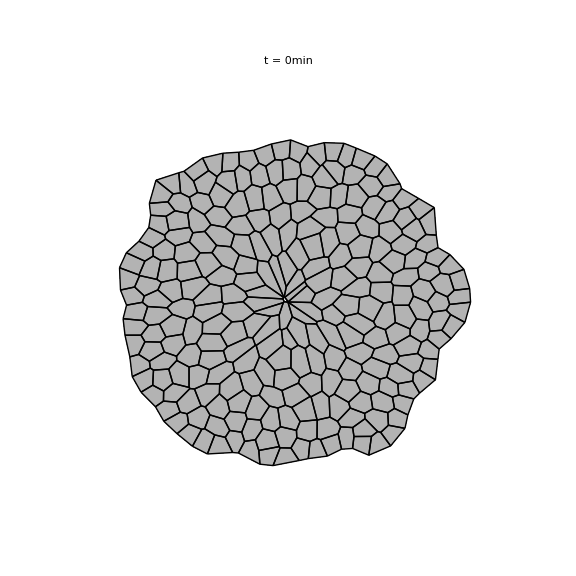

```mathematica
i = 1
Show[{(*Draw all cells-wound white,others grey*)Sequence@@Table[Graphics[{If[cell==woundNum,White,GrayLevel[0.7]],Polygon[vertexPositions[[voronoiData[[cell,2]]]]]}],{cell,Length[voronoiData]}],(*Draw edges*)Sequence@@Table[Graphics[{Thick,Black,Line[{vertexPositions[[voronoiData[[cell,2,j]]]],vertexPositions[[voronoiData[[cell,2,Mod[j,Length[voronoiData[[cell,2]]]]+1]]]]}]}],{cell,Length[voronoiData]},{j,Length[voronoiData[[cell,2]]]}]},PlotRange->{{-1.25 a,1.25 a},{-1.25 b,1.25 b}},PlotLabel->Style[StringJoin["t = ",ToString[Round[(i-1)]],"min"],Black,Bold,FontSize->20],ImageSize->Large]
```

```mathematica
(*used to recreate movie from exported traectories*)
a = 225;
b = 225;
importedRaw=Import["C:\\Users\\kaden\\Downloads\\finished_undergrad\\mathematica\\trajectoriesmovie2cont.csv"];
importedTrajectories=ToExpression[importedRaw];

(*Identify the largest cell at t=0 (first frame)*)
firstFrameVertices=importedTrajectories[[1,1]];
firstFrameVoronoi=importedTrajectories[[1,2]];

(*Calculate area for each cell*)
cellAreas=Table[cellVertices=firstFrameVertices[[firstFrameVoronoi[[cell,2]]]];
Area[Polygon[cellVertices]],{cell,Length[firstFrameVoronoi]}];

(*Find the cell with maximum area*)
woundNum=First[Ordering[cellAreas,-1]];

Print["Wound cell identified: Cell #",woundNum," with area ",Max[cellAreas]];

(*Create diagrams with wound highlighted in white,others in grey*)
diagramsFromImport=Table[vertexPositions=importedTrajectories[[i,1]];
voronoiData=importedTrajectories[[i,2]];
Show[{(*Draw all cells-wound white,others grey*)Sequence@@Table[Graphics[{If[cell==woundNum,White,GrayLevel[0.7]],Polygon[vertexPositions[[voronoiData[[cell,2]]]]]}],{cell,Length[voronoiData]}],(*Draw edges*)Sequence@@Table[Graphics[{Thick,Black,Line[{vertexPositions[[voronoiData[[cell,2,j]]]],vertexPositions[[voronoiData[[cell,2,Mod[j,Length[voronoiData[[cell,2]]]]+1]]]]}]}],{cell,Length[voronoiData]},{j,Length[voronoiData[[cell,2]]]}]},PlotRange->{{-1.25 a,1.25 a},{-1.25 b,1.25 b}},PlotLabel->Style[StringJoin["t = ",ToString[Round[(i-1)]],"min"],Black,Bold,FontSize->20],ImageSize->Large],{i,Length[importedTrajectories]}];


(*Export movie*)
Export["trajectoriesmoviecontwhite.gif",diagramsFromImport,Background->White]
```

Wound cell identified: Cell #1 with area 49943.5

trajectoriesmoviecontwhite.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["trajectoriesmoviecont.gif"]]]
```

```mathematica
areas=Table[
solNum = getSolNum[tt,solutionTable2]-1;
{tt,getCellArea[woundNum,Subscript[cellularVoronoiDiagrams, solNum],solutionTable2[[solNum+1]]/.t->tt]}

,{tt,0,tHealed,60}];
```

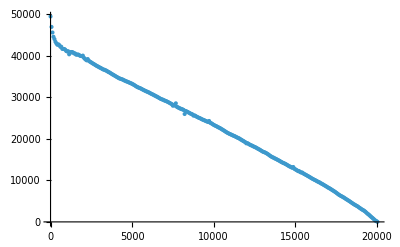

```mathematica
ListPlot[areas]
```

```mathematica
Export["area4syncdata.csv",areas,OverwriteTarget ->"KeepBoth"]
```

area4syncdata.csv

```mathematica
areas1 = Import["C:\\Users\\kaden\\Downloads\\finished_undergrad\\mathematica\\area4syncdata.csv"];
areas = Import["C:\\Users\\kaden\\Downloads\\finished_undergrad\\mathematica\\area4contdata.csv"];
```

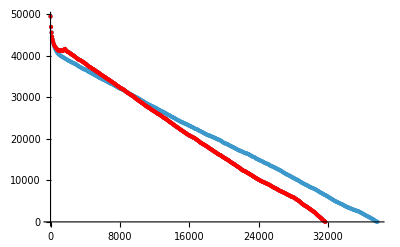

```mathematica
Show[{ListPlot[areas],ListPlot[Style[#,Red]&/@areas1]}]
```

```mathematica
Internal`RemoveHandler["Message",messageHandler]
```

messageHandler::shdw: Symbol messageHandler appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

### Figure Generation

38940

0.577812

0.668721

0.488444

0.813559

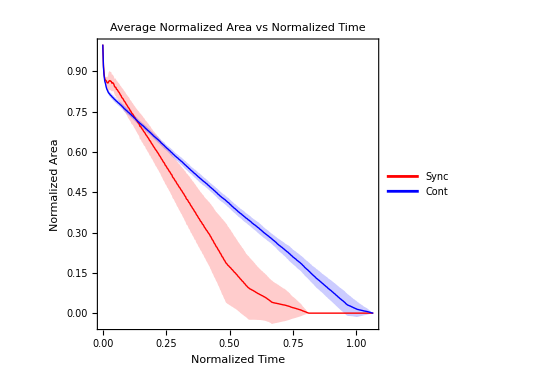

```mathematica
(*Base path*)basePath="C:\\Users\\kaden\\Downloads\\finished_undergrad\\mathematica\\area";
ttHeal=Table[(*Construct file paths for sync and cont*)syncPath=basePath<>ToString[num]<>"syncdata.csv";
contPath=basePath<>ToString[num]<>"contdata.csv";
(*Import the data*)syncData=Import[syncPath];
contData=Import[contPath];
(*Assuming data is {time,area} pairs or columns*)syncPoints=syncData;
contPoints=contData;
(*Get the last time point in sync for normalization*)
Max[contPoints[[All,1]]]
,{num,1,4}];
norm = Mean[ttHeal]
(*Import and process data for each number (9-12)*)
processedData=Table[(*Construct file paths for sync and cont*)syncPath=basePath<>ToString[num]<>"syncdata.csv";
contPath=basePath<>ToString[num]<>"contdata.csv";
(*Import the data*)
syncData=Import[syncPath];
contData=Import[contPath];
(*Assuming data is {time,area} pairs or columns*)syncPoints=syncData;
contPoints=contData;
(*Get the last time point in sync for normalization*)
lastContTime=Max[contPoints[[All,1]]];
lastSyncTime = Max[syncPoints[[All,1]]];
Print[N[lastSyncTime/norm]];
totArea = syncPoints[[1,2]];
syncNorm = {#[[1]]/norm,#[[2]]/totArea}&/@syncPoints;
(*Normalize time points to last sync time*)
contNorm={#[[1]]/norm,#[[2]]/totArea}&/@contPoints;
(*Return normalized data*)
{syncNorm,contNorm},{num,1,4}];
(*Function to pad datasets to same length*)
timeStep = Table[Table[processedData[[i]][[j]][[2]][[1]]-processedData[[i]][[j]][[1]][[1]],{j,Length[processedData[[i]]]}],{i,Length[processedData]}];
timeStepMax = Max[timeStep];
tStop = Max[processedData[[All,All,All,1]]];
binned[data_, width_,tStop_]:=
(
Table[
{i,Pick[data,IntervalMemberQ[Interval[{i,(i+1)}],data[[All,1]]]][[All,2]]}
,{i,0,tStop,width}]
)
meanSEM[dataBinned_]:=
(
{#[[1]][[1]],Mean[PadRight[#[[All,2]],4]],StandardDeviation[PadRight[#[[All,2]],4]]}&/@dataBinned
)
(*Create polygons for error bars with transparency*)
makeErrorBand[meanSEM_,color_]:=
(upper={#[[1]],#[[2]]+#[[3]]}&/@meanSEM;
lower=Reverse[{#[[1]],#[[2]]-#[[3]]}&/@meanSEM];
{Opacity[0.2],color,Polygon[Join[upper,lower]]}
)
sortedData = Table[
Table[
If[Length[#[[2]]]>0,{#[[1]],#[[2]][[1]]},{#[[1]],0}]&/@binned[processedData[[i,j]],timeStepMax*1.001,tStop]
,{j,Length[processedData[[i]]]}]
,{i,Length[processedData]}];
sortedDataTranspose =Transpose[sortedData];
superSorted =Table[Transpose[sortedDataTranspose[[i]]],{i,Length[sortedDataTranspose]}];
meanStE = Table[meanSEM[superSorted[[i]]],{i,Length[sortedDataTranspose]}];
colorList = {Red,Blue};
errorBands = Table[makeErrorBand[meanStE[[i]],colorList[[i]]],{i,Length[meanStE]}];

(*Plot with transparent error bands and mean lines*)
Style[Show[Graphics[errorBands],ListPlot[{meanStE[[1,All,{1,2}]],meanStE[[2,All,{1,2}]]},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},Joined->True,PlotLegends->{"Sync","Cont"}],PlotRange->Full,Frame->True,FrameLabel->{"Normalized Time","Normalized Area"},PlotLabel->"Average Normalized Area vs Normalized Time"],FontColor->Black]
```

```mathematica
Export["areavstimever2.svg",%,Background->White]
```

areavstimever2.svg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["areavstime.svg"]]]
```

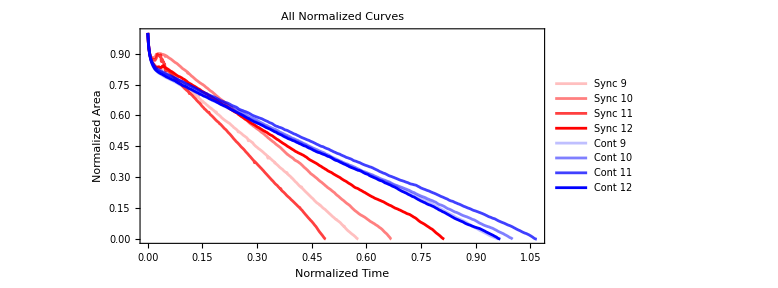

```mathematica
(*Extract all individual curves*)allSyncCurves=processedData[[All,1]];  (*All sync curves*)
allContCurves=processedData[[All,2]];  (*All cont curves*)

(*Plot all curves*)
ListPlot[Join[allSyncCurves,allContCurves],PlotStyle->Join[Table[Directive[Red,Opacity[i/Length[allSyncCurves]]],{i,Length[allSyncCurves]}],Table[Directive[Blue,Opacity[i/Length[allContCurves]]],{i,Length[allContCurves]}]],Joined->True,PlotRange->{All,All},AspectRatio->1/2,Frame->True,FrameLabel->{"Normalized Time","Normalized Area"},PlotLabel->"All Normalized Curves",PlotLegends->Join[Table["Sync "<>ToString[i],{i,9,12}],Table["Cont "<>ToString[i],{i,9,12}]],ImageSize->Large]
```